# UpSetChart Tests

```mathematica
Quit[];
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

First::normal: Nonatomic expression expected at position 1 in First[spacing].

Last::normal: Nonatomic expression expected at position 1 in Last[spacing].

First::normal: Nonatomic expression expected at position 1 in First[spacing].

Last::normal: Nonatomic expression expected at position 1 in Last[spacing].

```mathematica
<<UpSetChart`TestData`
sets=DummyData[2]
```

<|a→{11,37},b→{42,38,72,54,70,38,5,34,45,67,89,59,83,70,19,17,86,37,77,85},c→{20,12,22},d→{55,78,59,87,33},e→{61,75,8,10,16,60,45,16,13,34,62,86,97,46,44,37,3,43},f→{69,78,5,41,49,24,16,36,46,51,12,87,92,35},g→{21,62,82,56,31,72,4,45,1,100,74,47,13,23,88,36,84},h→{15,34,77,73,20,60,93,84,56,45,34,81,16,91,86,81,41,81,21,34,72,18,18,25,36,68},i→{80,39,59,22,99,69,27,5,46,9,81,18,19,27,30,1,48,34,54},j→{8,80,17,92,32,68,49,95,5,67,3,7,3,46,83,15,21,12,42,13,21,91,7,78,42,67}|>

<|a→{18,60,16,13,25,62,59,58,73,29},b→{69,61},c→{44,2,3,45,24},d→{3,8,19,93,14,1,81,40,90,96,82,87,45,43,98,86,65,4},e→{36,3,31,91,16,39,5,71},f→{79,43,41,77,90,5,3,27,24,74,80},g→{56,90,79,67,58,40,88,9,55,3,53,16,97,85,45,75,42,63},h→{45,1,80,23,61,90},i→{32,50,96,58,65,81,79,86,20,88,56,14,53,92,77,46},j→{93,46,52,100,11,48,25,26,31,12,90,10,39,64,87,95,86,79,49,69},k→{16,85,75,53,68,64,42,98,43,77,90,48,37,94,18,91,58,7,12,5,6},l→{65,95,26,15},m→{75,62,57,20,55,67,73,48,18,58,71,44,26,30,47,79,78,25},n→{51,34,50,81,84,15,100,96,61,12,68,74,59,87,41,62,47,75,26,60,44,89,66,24,58,40},o→{55,21,32,52,51,62,54,88,84,25,50,24,99,30,85,57,74,80,89},p→{54,78,61,82,43,8,12,38,22,89,35,18,3,65,92,15,1,55,66,16,72,24,67,84,87,44,69,49},q→{83,98,78,44,76},r→{27,95,44,40,25,76,77,64},s→{84,92,44,96,39},t→{13,3,53,62,99,93}|>

```mathematica
Sort@Keys@sets
```

{Fruit,Green,Red,Tasty,Vegetable}

```mathematica
DynamicUpSetChart[sets,"TabbedByComparisonsDegreeQ"->True,"ImageSize"->{Automatic,100}]
```

## The Packages of UpSetChart

```mathematica
UpSetChart`Graphics`Utilities`GraphicComponents[sets]
```

UpSetChart`Graphics`Utilities`GraphicComponents[<|Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Tasty→{Kiwi,Pear},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Vegetable→{Cucumber,Pickle}|>]

```mathematica
UpSetChart[sets]
```

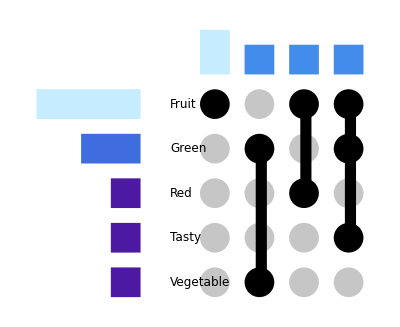
```mathematica
-Graphics-//InputForm
```

```mathematica
2^20
```

1048576

```mathematica
Options[BarChart][[;;,1]]
```

{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BarOrigin,BarSpacing,BaselinePosition,BaseStyle,ChartBaseStyle,ChartElementFunction,ChartElements,ChartLabels,ChartLayout,ChartLegends,ChartStyle,ColorFunction,ColorFunctionScaling,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,Joined,LabelingFunction,LabelingSize,LabelStyle,LegendAppearance,Method,PerformanceGoal,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PlotTheme,PreserveImageOptions,Prolog,RotateLabel,ScalingFunctions,TargetUnits,Ticks,TicksStyle}

```mathematica
d=RandomData[20];
```

```mathematica
p=UpSetChart[d,"DropEmpty"->True, "SetSortBy"->"Cardinality", "IntersectionSortBy"-> "Cardinality","TabbedByComparisonsDegreeQ"->True,"ImageSize"->{Automatic, 250}]
```

12345

```mathematica
upc=UpSetChart[sets]
```

-Graphics-

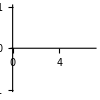
-Graphics-
-Graphics-

```mathematica
Graphics[
{
upc[[1]],
 Inset[
Graphics[{Opacity[0],Line[{{0,0},{7,0}}]},
Axes->{True, False},
ImageMargins->0,
ImagePadding->None,
ImageSize->{100,100},
AxesOrigin->{0,0}
(*,PlotRange->{{0,7},{0,3}}*)
(*,ImageSize->{7,100}*),
Ticks->{{{0,7}}}
],
{0,16},{0,0}
]
},
ImageMargins->0,
ImageSize->Automatic,
ImagePadding->None
]
```

```mathematica
EnsureLa
```

```mathematica
res=Table[
UpSetChart[sets, 
"DropEmpty"->dropEmpty, 
"SetSortBy"->setSort,
 "IntersectionSortBy"->compSort,
"TabbedByComparisonsDegreeQ"->False
], {dropEmpty, {True, False}}, {setSort, {"Name", "Cardinality"}}, {compSort, {"Name","Cardinality"}}
]
```

```mathematica
res2=Table[
UpSetChart[sets, 
"DropEmpty"->dropEmpty, 
"SetSortBy"->setSort,
 "IntersectionSortBy"->compSort,
"TabbedByComparisonsDegreeQ"->True,
"ImageSize"->{Automatic, 200}
], {dropEmpty, {True}}, {setSort, {"Name", "Cardinality"}}, {compSort, {"Name","Cardinality"}}
]
```

{{{123,123},{123,123}}}

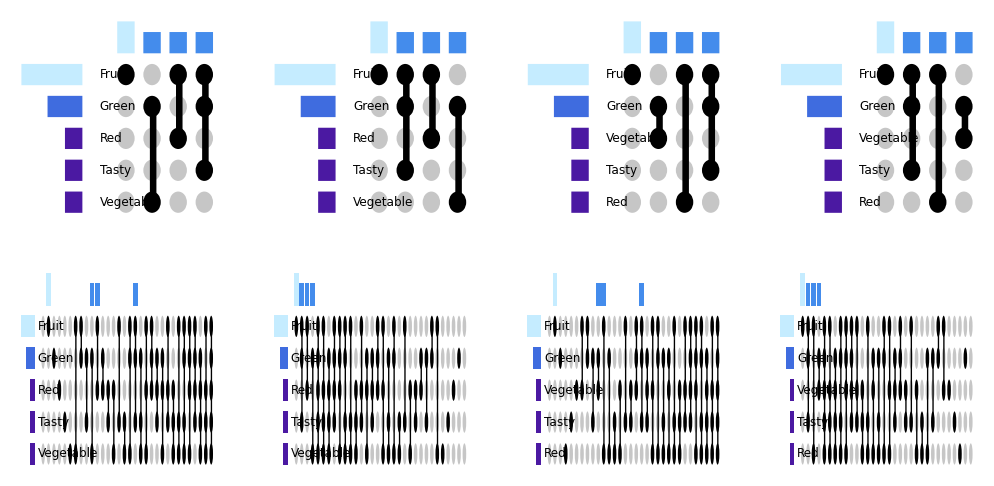

```mathematica
GraphicsGrid[Partition[Flatten[Join[res,res2]],{4}]]
```

```mathematica
UpSetChart[sets,"TabbedByComparisonsDegreeQ"->True ]
```

123

## Unique Intersections

```mathematica
(* Calculates the unique elements for the comparisons *)
<<UpSetChart`UniqueIntersections`
```

```mathematica
UniqueIntersections[<|"a"->{}|>]
```

<|sets→<|a→{}|>,setNames→{a},comparisons→{{},{a}},numberOfSets→1,elementsUniqueToComparisons→<|{}→{},{a}→{}|>|>

## Utilities

Utilities contains several conditional checkers and helpers.

```mathematica
(* Conditionals for types & passing down options *)
<<UpSetChart`Utilities`
```

```mathematica
EnsureLabeledSets[{{1,2,3},{2,3,4,4,4}}]
```

<|a→{1,2,3},b→{2,3,4}|>

```mathematica
EnsureLabeledSets[{{},{}}]
```

<|a→{},b→{}|>

```mathematica
sets={{1,2,3},{2,3,4,4,4}};
ListOfListsQ[sets]
LabeledSetsQ[sets]
LabeledSetsQ[EnsureLabeledSets[sets]]
```

True

False

True

## Calculations

While Unique Intersections does all the calculations we need for this chart, the chart may want us to sort and filter results as well.
This “super” function does this.

```mathematica
(* Calls UniqueIntersections and sorts & filters data *)
<<UpSetChart`Calculations`
```

```mathematica
calc=CalcThenSortAndFilter[sets]
```

<|sets→<|j→{8,80,17,92,32,68,49,95,5,67,3,7,3,46,83,15,21,12,42,13,21,91,7,78,42,67},i→{80,39,59,22,99,69,27,5,46,9,81,18,19,27,30,1,48,34,54},h→{15,34,77,73,20,60,93,84,56,45,34,81,16,91,86,81,41,81,21,34,72,18,18,25,36,68},g→{21,62,82,56,31,72,4,45,1,100,74,47,13,23,88,36,84},f→{69,78,5,41,49,24,16,36,46,51,12,87,92,35},e→{61,75,8,10,16,60,45,16,13,34,62,86,97,46,44,37,3,43},d→{55,78,59,87,33},c→{20,12,22},b→{42,38,72,54,70,38,5,34,45,67,89,59,83,70,19,17,86,37,77,85},a→{11,37}|>,comparisons→<|{a}→{11},{b}→{38,70,85,89},{d}→{33,55},{e}→{10,43,44,61,75,97},{f}→{24,35,51},{g}→{4,23,31,47,74,82,88,100},{h}→{25,73,93},{i}→{9,27,30,39,48,99},{j}→{7,32,95},{b,h}→{77},{b,i}→{19,54},{b,j}→{17,42,67,83},{c,h}→{20},{c,i}→{22},{d,f}→{87},{e,g}→{62},{e,h}→{60},{e,j}→{3,8},{f,h}→{41},{f,i}→{69},{f,j}→{49,92},{g,h}→{56,84},{g,i}→{1},{h,i}→{18,81},{h,j}→{15,68,91},{i,j}→{80},{a,b,e}→{37},{b,d,i}→{59},{b,e,h}→{86},{b,g,h}→{72},{c,f,j}→{12},{d,f,j}→{78},{e,f,h}→{16},{e,g,j}→{13},{f,g,h}→{36},{g,h,j}→{21},{b,e,g,h}→{45},{b,e,h,i}→{34},{b,f,i,j}→{5},{e,f,i,j}→{46}|>|>

### Calculation Utilities

```mathematica
(* Sort & filter functions *)
<<UpSetChart`Calculations`Utilities`
```

## Graphics

```mathematica
(* Returns the graphics for UpSetChart *)
<<UpSetChart`Graphics`
```

Graphics is a wrapper GraphicComponents returning the Graphic Item. Allows for processing of the Options before passing them

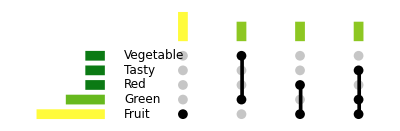

```mathematica
UpSetGraphics[
	calc["sets"], 
	calc["comparisons"],
	"ColorGradient"->"AvocadoColors",
	"ComponentSpacing"->{1,1},
	"IndicatorRadius"->0.5,
	"IndicatorSpacing"->{5,1/2}
]
```

### Utilities

Graphic Utilities is a wrapper over the four main components and returns them as a list.

```mathematica
(* Returns each components for the UpSetChart *)
<<UpSetChart`Graphics`Utilities`
```

```mathematica
gc=GraphicComponents[calc["sets"], calc["comparisons"],"IndicatorRadius"->1];
```

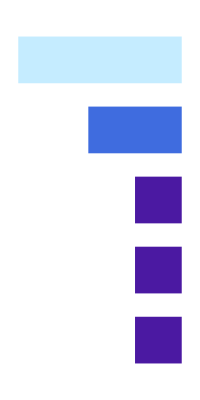
ImageSize[-Graphics-]

```mathematica
ImageSize@Graphics@gc[[1]]
```

```mathematica
<<GraphicsInformation`
```

```mathematica
Graphics[{Translate[{{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,2},{7,4}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,5},{7,7}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,8},{7,10}]},{RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858],Rectangle[{3,11},{7,13}]},{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,14},{7,16}]}},{0,0}]}]//GraphicsInformation
```

{ImagePadding→{{0.,1.},{1.,5.68434×10^-14}},ImageSize→{221.078,432.},PlotRangeSize→{220.078,431.},ImagePaddingSize→{1.,1.},PlotRange→{{-0.145833,7.14583},{1.86,16.14}},BasePlotRange→{{0.,7.},{2.,16.}}}

```mathematica
Graphics[{Translate[{{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,2},{7,4}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,5},{7,7}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,8},{7,10}]},{RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858],Rectangle[{3,11},{7,13}]},{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,14},{7,16}]}},{0,0}]}]
```

-Graphics-

```mathematica
Graphics[{Translate[{{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,2},{7,4}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,5},{7,7}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,8},{7,10}]},{RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858],Rectangle[{3,11},{7,13}]},{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,14},{7,16}]}},{0,0}],Point[{10,0}],Inset[Graphics[{},Axes->{True,False},Ticks->{Charting`ScaledTicks["Reverse"],None},PlotRange->{{-7,0},{1,16}}],{7,0},{0,0},Offset@{500,370}]},ImagePadding->0]
```

-Graphics-

```mathematica
Graphics[{Translate[{{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,2},{7,4}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,5},{7,7}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,8},{7,10}]},{RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858],Rectangle[{3,11},{7,13}]},{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,14},{7,16}]}},{0,0}],Point[{10,0}],Inset[Graphics[{},AspectRatio->1/1,Axes->{True,False},Ticks->{Charting`ScaledTicks["Reverse"],None},PlotRange->{{-7,0},{1,16}}],{7,0},{0,0},1{7,15}]},ImagePadding->0,AspectRatio->1/1]
```

-Graphics-

```mathematica
Graphics[gc[[2]]]//GraphicsInformation
```

{ImagePadding→{{0.,48.7755},{1.,4.9738×10^-14}},ImageSize→{360.,94.4353},PlotRangeSize→{311.224,93.4353},ImagePaddingSize→{48.7755,1.},PlotRange→{{10.7708,22.2292},{16.78,20.22}},BasePlotRange→{{11.,22.},{17.,20.}}}

```mathematica
Graphics[{gc[[2]],Point[{11,17}],Inset[Graphics[{},AspectRatio->1/1,Axes->{False,True},PlotRange->{{11.,22.},{17.,20.}}],{0,0},{0,0},{1,3}]},ImagePadding->0,AspectRatio->1/1]
```

-Graphics-

```mathematica
Graphics[gc
```

-Graphics-

```mathematica
Show[
Graphics[{},
 Inset[
gc[[1]],
Axes->{True, False},
ImageMargins->0,
ImagePadding->None,
ImageSize->{100,100},
AxesOrigin->{0,0}
(*,ImageSize->{7,100}*)
]],
{0,16},{0,0}
],
Graphics[gc[[2]]],
Graphics[gc[[3]]],
Graphics[gc[[4]]]
]
```

```mathematica
Graphics[{
Inset[Graphics[gc[[1]], Axes->{True,False}]],
Inset[Graphics[gc[[2]], Axes->{False,True}]],
Inset[Graphics[gc[[3]]]],
Inset[Graphics[gc[[4]]]]
}
]
```

Part::partw: Part 4 of GraphicComponents[<|Vegetable→{Cucumber,Pickle},Tasty→{Kiwi,Pear},Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot}|>,<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>,IndicatorRadius→1] does not exist.

-Graphics-

### Comparisons Bar Chart

Comparisons Bar Chart produces the bar chart for the cardinality of the set comparisons

```mathematica
(* Components for charts *)
<<UpSetChart`Graphics`ComparisonsBarChart`
```

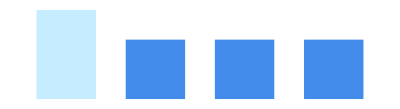

```mathematica
ComparisonsBarChart[calc["comparisons"],
 Max[Length/@calc["comparisons"]], Keys@calc["sets"]
]//Graphics[#,ImageSize->Tiny]&
```

### Grid Indicator

Grid Indicator produces the bubble heatmap which indicates which sets correspond to which comparisons

```mathematica
<<UpSetChart`Graphics`IndicatorGrid`
```

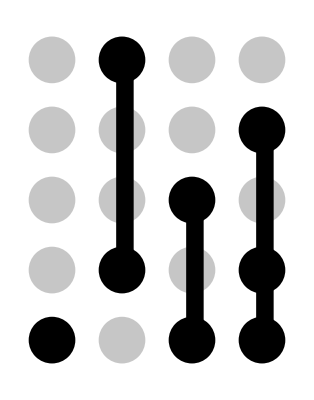

```mathematica
IndicatorGrid[Keys[calc["sets"]],Keys[calc["comparisons"]]]//Graphics[#,ImageSize->Tiny]&
```

### Sets Bar Chart

Produces the Bar Chart for the cardinality of sets

```mathematica
<<UpSetChart`Graphics`SetsBarChart`
```

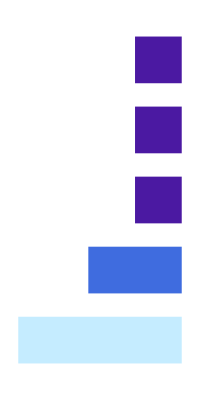

```mathematica
SetsBarChart[calc["sets"], Keys[calc["sets"]], Max[Length/@calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

### Labels

Produces the labels of the sets. Works best with short labels

```mathematica
<<UpSetChart`Graphics`SetsLabels`
```

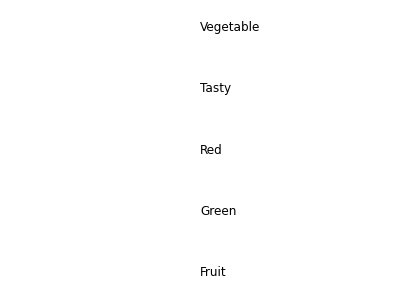

```mathematica
SetsLabels[ Keys[calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```